```mathematica
ClearAll["Global`*"]
ClearSystemCache[]
$PrePrint=MatrixForm;
```

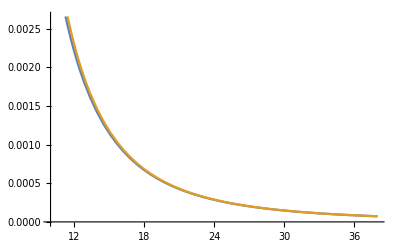

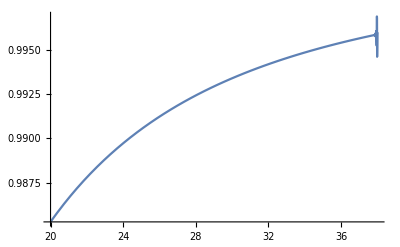

```mathematica
f[u_]:=(-2 u+Sqrt[2 Pi] (1+u u) Exp[u^2/2] Erfc[u/Sqrt[2]]);
g[u_]:=(4/u^3);
Plot[{f[u],g[u]},{u,10,38}]
Plot[f[u]/g[u],{u,20,38}]
```

```mathematica
error=Integrate[g[u],{u,38,Infinity}]
N[error]
```

1/722

0.00138504

```mathematica
Series[f[u],{u,Infinity,11}]
```

4/u^3-24/u^5+180/u^7-1680/u^9+18900/u^11+O[1/u]^12

```mathematica
h[u_]:=((4-24/u^2+180/u^4)/u^3);
error=Integrate[h[u],{u,38,Infinity}]
N[error]
```

2080819/1505468192

0.00138217

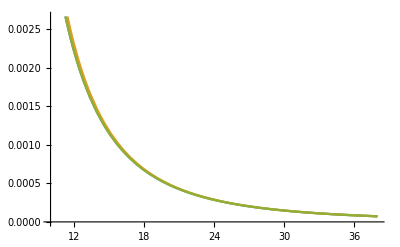

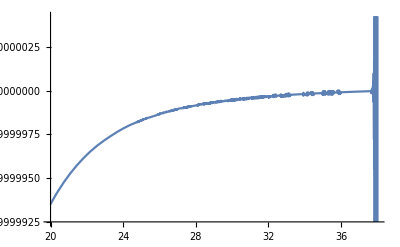

```mathematica
Plot[{f[u],g[u],h[u]},{u,10,38}]
Plot[f[u]/h[u],{u,20,38}]
```